```mathematica
url="http://pages.mtu.edu/~dnaneet/thermo/hptr.txt";
datasetDirty=Import[url, "Data"];
(*names={'celcius','bar','region','kJPerKg'}*)
s=Dimensions[dataset][[1]];
dataset=Select[dataset, #[[3]]≠ 0&]; (*Select only those rows and columns with non zero region*)
Take[dataset,5]
```

{{10,1,1,42.1174},{20,1,1,84.0118},{30,1,1,125.833},{40,1,1,167.623},{50,1,1,209.412}}

#### Data division

```mathematica
T=dataset[[2;;s,1]];
P=dataset[[2;;s,2]];
r=dataset[[2;;s,3]]/.{0->"r0",1->"r1", 2->"r2", 3->"r3", 4->"r4", 5->"r5"};
h=dataset[[2;;s,4]];
```

```mathematica
regionIdentification=Thread[{T,P}];
mldata=RandomSample[Thread[regionIdentification->r]];
```

```mathematica
s=Dimensions[mldata][[1]];
training=mldata[[1;;Ceiling[0.7*s]]];
validation=mldata[[Ceiling[0.7*s];;s]];
```

#### Auto classifier choice

```mathematica
cThermo0=Classify[training,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[cThermo0]
```

Classifier information
Input type | {Numerical,Numerical}
Classes | ,,r1r2r3r5
Method | GradientBoostedTrees
Accuracy | 98.5 % ± 0.74 %
Loss | 0.0366 ± 0.0072
Single evaluation time | 11.8 ms/example
Batch evaluation speed | 6.13 examples/ms
Classifier memory | 874. kB
Training examples used | 6433 examples
Training time | 9.8 s
 |

ClassifierMeasurementsObject[…]

0.995285

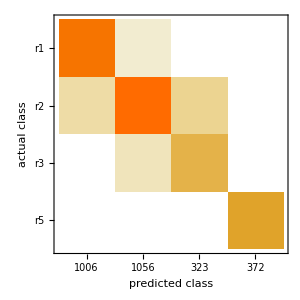

```mathematica
cm0=ClassifierMeasurements[cThermo0,validation]
cm0["Accuracy"]
cm0["ConfusionMatrixPlot"]
```

#### Decision Tree

```mathematica
cThermo1=Classify[training,Method->"DecisionTree",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[cThermo1]
```

Classifier information
Input type | {Numerical,Numerical}
Classes | ,,r1r2r3r5
Method | DecisionTree
Accuracy | 98.4 % ± 0.36 %
Loss | 0.0567 ± 0.0075
Single evaluation time | 1.3 ms/example
Batch evaluation speed | 309. examples/ms
Classifier memory | 130. kB
Training examples used | 6433 examples
Training time | 1.98 s
 |

ClassifierMeasurementsObject[…]

0.982227

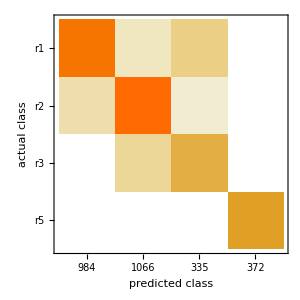

```mathematica
cm1=ClassifierMeasurements[cThermo1,validation]
cm1["Accuracy"]
cm1["ConfusionMatrixPlot"]
```